# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
```

```mathematica
<<UpSetChart`Data`
sets=DummyData[1]
```

<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>

## The Packages of UpSetChart

```mathematica
<<UpSetChart`
```

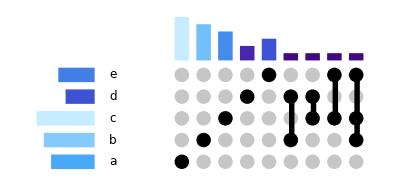

```mathematica
UpSetChart[sets]
```

```mathematica
MatchQ[UpSetChart[sets],UpSetChart[EnsureLabeledSets[sets]]]
```

True

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[sets]
```

<|sets→<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,setNames→{a,b,c,d,e},comparisons→{{},{a},{b},{c},{d},{e},{a,b},{a,c},{a,d},{a,e},{b,c},{b,d},{b,e},{c,d},{c,e},{d,e},{a,b,c},{a,b,d},{a,b,e},{a,c,d},{a,c,e},{a,d,e},{b,c,d},{b,c,e},{b,d,e},{c,d,e},{a,b,c,d},{a,b,c,e},{a,b,d,e},{a,c,d,e},{b,c,d,e},{a,b,c,d,e}},numberOfSets→5,elementsUniqueToComparisons→<|{}→{},{a,b,c,d,e}→{},{a,b,c,d}→{},{a,b,c,e}→{},{a,b,d,e}→{},{a,c,d,e}→{},{b,c,d,e}→{},{a,b,c}→{},{a,b,d}→{},{a,b,e}→{},{a,c,d}→{},{a,c,e}→{},{a,d,e}→{},{b,c,d}→{},{b,c,e}→{87},{b,d,e}→{},{c,d,e}→{},{a,b}→{},{a,c}→{},{a,d}→{},{a,e}→{},{b,c}→{},{b,d}→{90},{b,e}→{},{c,d}→{6},{c,e}→{15},{d,e}→{},{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97}|>|>

## Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
ListOfListsQ[sets]
LabeledSetsQ[sets]
```

ListOfListsQ[<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>]

True

## Calculations

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Green→{Kiwi,Pear,Cucumber,Pickle},Red→{Strawberry,Apple},Tasty→{Kiwi,Pear},Vegetable→{Cucumber,Pickle}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`CalculationsUtilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

Graphics is a wrapper GraphicComponents returning the Graphic Item. Allows for processing of the Options before passing them

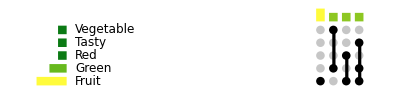

```mathematica
UpSetGraphics[calc["sets"], calc["comparisons"],"ColorGradient"->"AvocadoColors", "ComponentSpacing"->{1,1},"IndicatorRadius"->1,"IndicatorSpacing"->{1,1}]
```

### Utilities

Graphic Utilities is a wrapper over the four main components and returns them as a list.

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`GraphicsUtilities`
```

```mathematica
GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1]
```

{{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{0,2},{7,4}]},{RGBColor[0.24882928571428573, 0.42314085714285715, 0.8732312857142858],Rectangle[{3,5},{7,7}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,8},{7,10}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,11},{7,13}]},{RGBColor[0.29575928571428567, 0.09888902857142857, 0.634997],Rectangle[{5,14},{7,16}]}},{{RGBColor[0.772061, 0.92462, 0.998703],Rectangle[{65,17},{67,20}]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[{68,17},{70,19}]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[{71,17},{73,19}]},{RGBColor[0.26669366666666666, 0.550462, 0.926485],Rectangle[{74,17},{76,19}]}},{Text[Fruit,{9,3},{-1,0}],Text[Green,{9,6},{-1,0}],Text[Red,{9,9},{-1,0}],Text[Tasty,{9,12},{-1,0}],Text[Vegetable,{9,15},{-1,0}]},{{{{GrayLevel[0],Disk[{66,3},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{69,3},1]},{GrayLevel[0],Disk[{72,3},1]},{GrayLevel[0],Disk[{75,3},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{66,6},1]},{GrayLevel[0],Disk[{69,6},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{72,6},1]},{GrayLevel[0],Disk[{75,6},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{66,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{69,9},1]},{GrayLevel[0],Disk[{72,9},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{75,9},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{66,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{69,12},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{72,12},1]},{GrayLevel[0],Disk[{75,12},1]}},{{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{66,15},1]},{GrayLevel[0],Disk[{69,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{72,15},1]},{RGBColor[0.7777777777777778, 0.7777777777777778, 0.7777777777777778],Disk[{75,15},1]}}},{{GrayLevel[0],Rectangle[{263/4,3},{133/2,3}]},{GrayLevel[0],Rectangle[{275/4,6},{139/2,15}]},{GrayLevel[0],Rectangle[{287/4,3},{145/2,9}]},{GrayLevel[0],Rectangle[{299/4,3},{151/2,12}]}}}}

```mathematica
t={Text[Style["a",12], {-1,0}],Text[Style["adas",12], {-1,0}]};
a=Graphics[t]
ImageDimensions[ImageCrop[a]]
Rasterize[t,"RasterSize"]
```

```mathematica
RectangleChart
```

-Graphics-

{25,9}

{293,17}

### Comparisons Bar Chart

Comparisons Bar Chart produces the bar chart for the cardinality of the set comparisons

```mathematica
(* Components for charts *)
<<UpSetChart`GraphicsUtilitiesComparisonsBarChart`
```

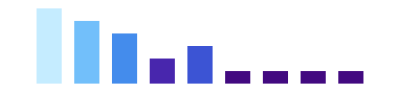

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

### Grid Indicator

Grid Indicator produces the bubble heatmap which indicates which sets correspond to which comparisons

```mathematica
<<UpSetChart`GraphicsUtilitiesIndicatorGrid`
```

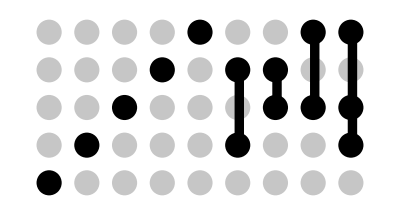

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

### Sets Bar Chart

Produces the Bar Chart for the cardinality of sets

```mathematica
<<UpSetChart`GraphicsUtilitiesSetsBarChart`
```

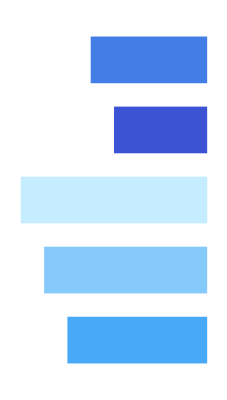

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

### Labels

Produces the labels of the sets. Works best with short labels

```mathematica
<<UpSetChart`GraphicsUtilitiesSetsLabels`
```

```mathematica
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

-Graphics-